```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection[JDBC["SQLite","/home/daniel/exp/loopspeed/log.db"]]
```

SQLConnection[…]

```mathematica
list=SQLExecute[conn,"SELECT name FROM log GROUP BY name"];
```

```mathematica
data=Table[{i[[1]],SQLExecute[conn,"SELECT size,time FROM log WHERE name='"<>ToString[i[[1]]]<>"' AND git!='fd7f0d3acd0cd14af4e7d9d51713dc0875e65ae0'"]},{i,list}];
```

```mathematica
lps=FindFit[Log[data[[#,2]]],Log[Exp[a] Exp[x]+b^2],{a,b},x]&/@Range[data//Length];
```

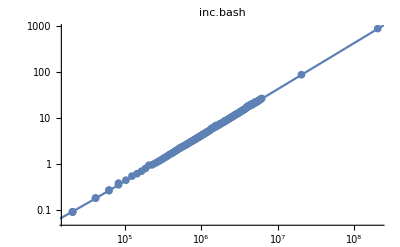
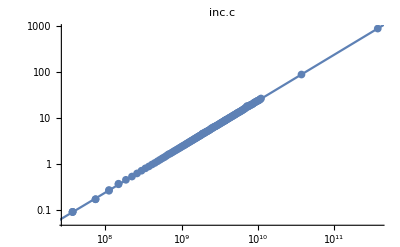
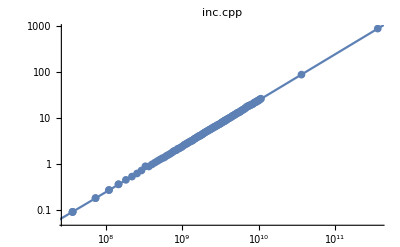
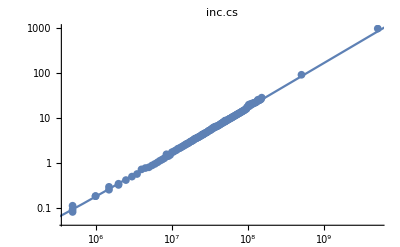
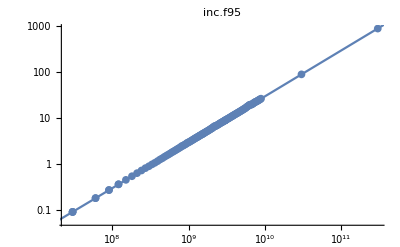
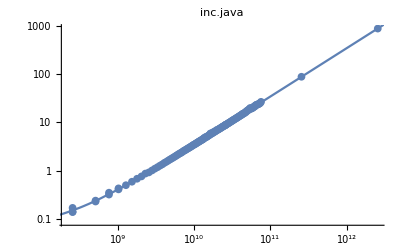
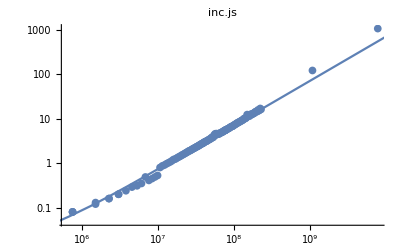
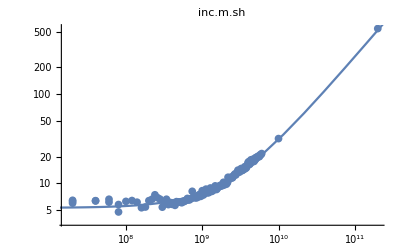

```mathematica
Table[Show[{ListLogLogPlot[{data[[i,2]]},PlotRange->Full,PlotLabel->data[[i,1]],BaseStyle->{FontSize->11}],LogLogPlot[Exp[a]x + b^2/.lps[[i]],{x,1,10^13}]}],{i,1,16}]
```

```mathematica
gitr=SQLExecute[conn,"SELECT git FROM log WHERE name='inc.r' GROUP BY git"];
```

```mathematica
gitr
```

{{1873b061eee49609e1684e2e96961862f742c133},{25ec2fff8fba379ab25d16d57b097e43f55bfd0d},{d1f050302c28aa8a837ec5453323df30cad9766e},{fd7f0d3acd0cd14af4e7d9d51713dc0875e65ae0}}

```mathematica
dr=SQLExecute[conn,"SELECT size,time FROM log WHERE name='inc.r' AND git='"<>ToString[#]<>"'"]&/@Flatten[gitr];
```

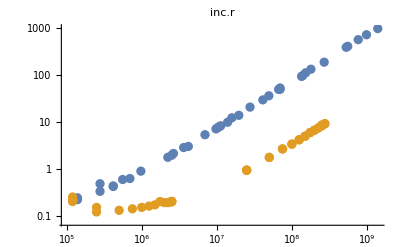

3.778

```mathematica
ListLogLogPlot[{Flatten[dr[[#]]&/@Range[3],1],dr[[4]]},PlotRange->Full,PlotLabel->data[[13,1]],BaseStyle->{FontSize->11}]
```

```mathematica
points=Floor[10^Range[0,4,0.01]]//DeleteDuplicates
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,50,51,52,53,54,56,57,58,60,61,63,64,66,67,69,70,72,74,75,77,79,81,83,85,87,89,91,93,95,97,100,102,104,107,109,112,114,117,120,123,125,128,131,134,138,141,144,147,151,154,158,162,165,169,173,177,181,186,190,194,199,204,208,213,218,223,229,234,239,245,251,257,263,269,275,281,288,295,301,309,316,323,331,338,346,354,363,371,380,389,398,407,416,426,436,446,457,467,478,489,501,512,524,537,549,562,575,588,602,616,630,645,660,676,691,707,724,741,758,776,794,812,831,851,870,891,912,933,954,977,1000,1023,1047,1071,1096,1122,1148,1174,1202,1230,1258,1288,1318,1348,1380,1412,1445,1479,1513,1548,1584,1621,1659,1698,1737,1778,1819,1862,1905,1949,1995,2041,2089,2137,2187,2238,2290,2344,2398,2454,2511,2570,2630,2691,2754,2818,2884,2951,3019,3090,3162,3235,3311,3388,3467,3548,3630,3715,3801,3890,3981,4073,4168,4265,4365,4466,4570,4677,4786,4897,5011,5128,5248,5370,5495,5623,5754,5888,6025,6165,6309,6456,6606,6760,6918,7079,7244,7413,7585,7762,7943,8128,8317,8511,8709,8912,9120,9332,9549,9772,10000}

```mathematica
Export["~/exp/loopspeed/list.txt",points]
```

~/exp/loopspeed/list.txt

```mathematica
Sum[Exp[a]x + b^2/.lps[[j]]/.x->139211*i,{i,points[[1;;200]]},{j,1,data//Length}]/86000
```

0.912821

```mathematica
Total[Flatten[data[[All,2,All,2]]]]/86000
```

0.267258

```mathematica
Length[data]
```

16

```mathematica
points//Length
```

279

```mathematica
points[[1;;200]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,50,51,52,53,54,56,57,58,60,61,63,64,66,67,69,70,72,74,75,77,79,81,83,85,87,89,91,93,95,97,100,102,104,107,109,112,114,117,120,123,125,128,131,134,138,141,144,147,151,154,158,162,165,169,173,177,181,186,190,194,199,204,208,213,218,223,229,234,239,245,251,257,263,269,275,281,288,295,301,309,316,323,331,338,346,354,363,371,380,389,398,407,416,426,436,446,457,467,478,489,501,512,524,537,549,562,575,588,602,616,630,645,660,676,691,707,724,741,758,776,794,812,831,851,870,891,912,933,954,977,1000,1023,1047,1071,1096,1122,1148,1174,1202,1230,1258,1288,1318,1348,1380,1412,1445,1479,1513,1548,1584,1621}